# Addition of Numbers

Here, we introduce a quantum circuit implementation of addition.

Make sure that Q3 is loaded.

```mathematica
<<Q3`
```

The two numbers to add are initially stored in quantum registers A and B, respectively. Temporary register T is to store the carrier bits.

```mathematica
Let[Qubit,A,B,T]
```

Suppose that we added two numbers each represented by  n binary digits. Note that we need one more bit in the temporary register T.

```mathematica
$n=3;
kk=Range[$n];
AA=A[kk,None];
BB=B[kk,None];
TT=T[Range[$n+1],None];
```

The result is stored in the register B. Note, however, that the last carrier bit is still stored in T only.

```mathematica
elm=Flatten@Table[
{CNOT[{A[k],B[k]},T[k+1]],
CNOT[A[k],B[k]],
CNOT[{B[k],T[k]},T[k+1]],
CNOT[T[k],B[k]]},
{k,$n}];
```

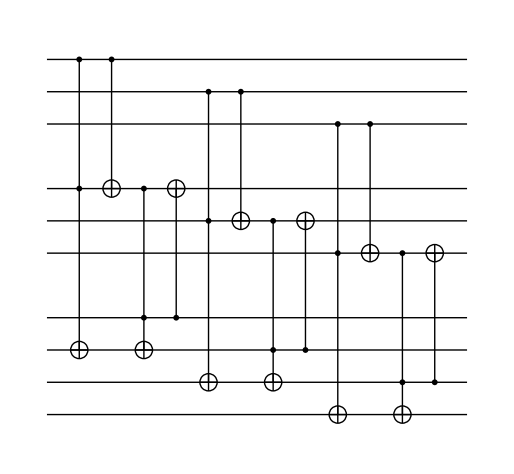

```mathematica
qc=QuantumCircuit[Sequence@@elm,
"Invisible"->{A[$n+1/2],B[$n+1/2]}
]
```

```mathematica
bs=Basis[AA,BB];
```

```mathematica
Timing[out=qc**bs;]
```

{3.49873,Null}

```mathematica
ab={FromDigits[Reverse[#@AA],2],FromDigits[Reverse[#@BB],2]}&/@bs;
cc=FromDigits[Reverse@Join[#@BB,#@T@{$n+1}],2]&/@out;
Thread[ab->cc]//TableForm
```

{0,0}→0
{0,4}→4
{0,2}→2
{0,6}→6
{0,1}→1
{0,5}→5
{0,3}→3
{0,7}→7
{4,0}→4
{4,4}→8
{4,2}→6
{4,6}→10
{4,1}→5
{4,5}→9
{4,3}→7
{4,7}→11
{2,0}→2
{2,4}→6
{2,2}→0
{2,6}→12
{2,1}→3
{2,5}→7
{2,3}→1
{2,7}→13
{6,0}→6
{6,4}→10
{6,2}→12
{6,6}→8
{6,1}→7
{6,5}→11
{6,3}→13
{6,7}→9
{1,0}→1
{1,4}→5
{1,2}→3
{1,6}→7
{1,1}→0
{1,5}→4
{1,3}→2
{1,7}→14
{5,0}→5
{5,4}→9
{5,2}→7
{5,6}→11
{5,1}→4
{5,5}→8
{5,3}→14
{5,7}→10
{3,0}→3
{3,4}→7
{3,2}→1
{3,6}→13
{3,1}→2
{3,5}→14
{3,3}→0
{3,7}→12
{7,0}→7
{7,4}→11
{7,2}→13
{7,6}→9
{7,1}→14
{7,5}→10
{7,3}→12
{7,7}→8

In fact, one can store the result spread over registers B and T. Then, one can remove some quantum circuit elements.

```mathematica
elm=Flatten@Table[
{CNOT[{A[k],B[k]},T[k+1]],
CNOT[A[k],B[k]],
CNOT[{B[k],T[k]},T[k+1]]},
{k,$n}];
```

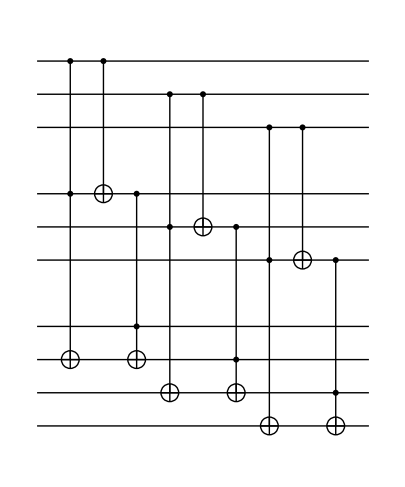

```mathematica
qc=QuantumCircuit[Sequence@@elm,
"Invisible"->{A[$n+1/2],B[$n+1/2]}
]
```

```mathematica
bs=Basis[AA,BB];
```

```mathematica
Timing[out=qc**bs;]
```

{2.27437,Null}

```mathematica
LogicalForm[Thread[bs->out]]//TableForm
```

0_A_10_A_20_A_30_B_10_B_20_B_30_T_20_T_30_T_4→0_A_10_A_20_A_30_B_10_B_20_B_30_T_20_T_30_T_4
0_A_10_A_20_A_30_B_10_B_21_B_30_T_20_T_30_T_4→0_A_10_A_20_A_30_B_10_B_21_B_30_T_20_T_30_T_4
0_A_10_A_20_A_30_B_11_B_20_B_30_T_20_T_30_T_4→0_A_10_A_20_A_30_B_11_B_20_B_30_T_20_T_30_T_4
0_A_10_A_20_A_30_B_11_B_21_B_30_T_20_T_30_T_4→0_A_10_A_20_A_30_B_11_B_21_B_30_T_20_T_30_T_4
0_A_10_A_20_A_31_B_10_B_20_B_30_T_20_T_30_T_4→0_A_10_A_20_A_31_B_10_B_20_B_30_T_20_T_30_T_4
0_A_10_A_20_A_31_B_10_B_21_B_30_T_20_T_30_T_4→0_A_10_A_20_A_31_B_10_B_21_B_30_T_20_T_30_T_4
0_A_10_A_20_A_31_B_11_B_20_B_30_T_20_T_30_T_4→0_A_10_A_20_A_31_B_11_B_20_B_30_T_20_T_30_T_4
0_A_10_A_20_A_31_B_11_B_21_B_30_T_20_T_30_T_4→0_A_10_A_20_A_31_B_11_B_21_B_30_T_20_T_30_T_4
0_A_10_A_21_A_30_B_10_B_20_B_30_T_20_T_30_T_4→0_A_10_A_21_A_30_B_10_B_21_B_30_T_20_T_30_T_4
0_A_10_A_21_A_30_B_10_B_21_B_30_T_20_T_30_T_4→0_A_10_A_21_A_30_B_10_B_20_B_30_T_20_T_31_T_4
0_A_10_A_21_A_30_B_11_B_20_B_30_T_20_T_30_T_4→0_A_10_A_21_A_30_B_11_B_21_B_30_T_20_T_30_T_4
0_A_10_A_21_A_30_B_11_B_21_B_30_T_20_T_30_T_4→0_A_10_A_21_A_30_B_11_B_20_B_30_T_20_T_31_T_4
0_A_10_A_21_A_31_B_10_B_20_B_30_T_20_T_30_T_4→0_A_10_A_21_A_31_B_10_B_21_B_30_T_20_T_30_T_4
0_A_10_A_21_A_31_B_10_B_21_B_30_T_20_T_30_T_4→0_A_10_A_21_A_31_B_10_B_20_B_30_T_20_T_31_T_4
0_A_10_A_21_A_31_B_11_B_20_B_30_T_20_T_30_T_4→0_A_10_A_21_A_31_B_11_B_21_B_30_T_20_T_30_T_4
0_A_10_A_21_A_31_B_11_B_21_B_30_T_20_T_30_T_4→0_A_10_A_21_A_31_B_11_B_20_B_30_T_20_T_31_T_4
0_A_11_A_20_A_30_B_10_B_20_B_30_T_20_T_30_T_4→0_A_11_A_20_A_30_B_11_B_20_B_30_T_20_T_30_T_4
0_A_11_A_20_A_30_B_10_B_21_B_30_T_20_T_30_T_4→0_A_11_A_20_A_30_B_11_B_21_B_30_T_20_T_30_T_4
0_A_11_A_20_A_30_B_11_B_20_B_30_T_20_T_30_T_4→0_A_11_A_20_A_30_B_10_B_20_B_30_T_21_T_30_T_4
0_A_11_A_20_A_30_B_11_B_21_B_30_T_20_T_30_T_4→0_A_11_A_20_A_30_B_10_B_21_B_30_T_21_T_31_T_4
0_A_11_A_20_A_31_B_10_B_20_B_30_T_20_T_30_T_4→0_A_11_A_20_A_31_B_11_B_20_B_30_T_20_T_30_T_4
0_A_11_A_20_A_31_B_10_B_21_B_30_T_20_T_30_T_4→0_A_11_A_20_A_31_B_11_B_21_B_30_T_20_T_30_T_4
0_A_11_A_20_A_31_B_11_B_20_B_30_T_20_T_30_T_4→0_A_11_A_20_A_31_B_10_B_20_B_30_T_21_T_30_T_4
0_A_11_A_20_A_31_B_11_B_21_B_30_T_20_T_30_T_4→0_A_11_A_20_A_31_B_10_B_21_B_30_T_21_T_31_T_4
0_A_11_A_21_A_30_B_10_B_20_B_30_T_20_T_30_T_4→0_A_11_A_21_A_30_B_11_B_21_B_30_T_20_T_30_T_4
0_A_11_A_21_A_30_B_10_B_21_B_30_T_20_T_30_T_4→0_A_11_A_21_A_30_B_11_B_20_B_30_T_20_T_31_T_4
0_A_11_A_21_A_30_B_11_B_20_B_30_T_20_T_30_T_4→0_A_11_A_21_A_30_B_10_B_21_B_30_T_21_T_31_T_4
0_A_11_A_21_A_30_B_11_B_21_B_30_T_20_T_30_T_4→0_A_11_A_21_A_30_B_10_B_20_B_30_T_21_T_31_T_4
0_A_11_A_21_A_31_B_10_B_20_B_30_T_20_T_30_T_4→0_A_11_A_21_A_31_B_11_B_21_B_30_T_20_T_30_T_4
0_A_11_A_21_A_31_B_10_B_21_B_30_T_20_T_30_T_4→0_A_11_A_21_A_31_B_11_B_20_B_30_T_20_T_31_T_4
0_A_11_A_21_A_31_B_11_B_20_B_30_T_20_T_30_T_4→0_A_11_A_21_A_31_B_10_B_21_B_30_T_21_T_31_T_4
0_A_11_A_21_A_31_B_11_B_21_B_30_T_20_T_30_T_4→0_A_11_A_21_A_31_B_10_B_20_B_30_T_21_T_31_T_4
1_A_10_A_20_A_30_B_10_B_20_B_30_T_20_T_30_T_4→1_A_10_A_20_A_31_B_10_B_20_B_30_T_20_T_30_T_4
1_A_10_A_20_A_30_B_10_B_21_B_30_T_20_T_30_T_4→1_A_10_A_20_A_31_B_10_B_21_B_30_T_20_T_30_T_4
1_A_10_A_20_A_30_B_11_B_20_B_30_T_20_T_30_T_4→1_A_10_A_20_A_31_B_11_B_20_B_30_T_20_T_30_T_4
1_A_10_A_20_A_30_B_11_B_21_B_30_T_20_T_30_T_4→1_A_10_A_20_A_31_B_11_B_21_B_30_T_20_T_30_T_4
1_A_10_A_20_A_31_B_10_B_20_B_30_T_20_T_30_T_4→1_A_10_A_20_A_30_B_10_B_20_B_31_T_20_T_30_T_4
1_A_10_A_20_A_31_B_10_B_21_B_30_T_20_T_30_T_4→1_A_10_A_20_A_30_B_10_B_21_B_31_T_20_T_30_T_4
1_A_10_A_20_A_31_B_11_B_20_B_30_T_20_T_30_T_4→1_A_10_A_20_A_30_B_11_B_20_B_31_T_21_T_30_T_4
1_A_10_A_20_A_31_B_11_B_21_B_30_T_20_T_30_T_4→1_A_10_A_20_A_30_B_11_B_21_B_31_T_21_T_31_T_4
1_A_10_A_21_A_30_B_10_B_20_B_30_T_20_T_30_T_4→1_A_10_A_21_A_31_B_10_B_21_B_30_T_20_T_30_T_4
1_A_10_A_21_A_30_B_10_B_21_B_30_T_20_T_30_T_4→1_A_10_A_21_A_31_B_10_B_20_B_30_T_20_T_31_T_4
1_A_10_A_21_A_30_B_11_B_20_B_30_T_20_T_30_T_4→1_A_10_A_21_A_31_B_11_B_21_B_30_T_20_T_30_T_4
1_A_10_A_21_A_30_B_11_B_21_B_30_T_20_T_30_T_4→1_A_10_A_21_A_31_B_11_B_20_B_30_T_20_T_31_T_4
1_A_10_A_21_A_31_B_10_B_20_B_30_T_20_T_30_T_4→1_A_10_A_21_A_30_B_10_B_21_B_31_T_20_T_30_T_4
1_A_10_A_21_A_31_B_10_B_21_B_30_T_20_T_30_T_4→1_A_10_A_21_A_30_B_10_B_20_B_31_T_20_T_31_T_4
1_A_10_A_21_A_31_B_11_B_20_B_30_T_20_T_30_T_4→1_A_10_A_21_A_30_B_11_B_21_B_31_T_21_T_31_T_4
1_A_10_A_21_A_31_B_11_B_21_B_30_T_20_T_30_T_4→1_A_10_A_21_A_30_B_11_B_20_B_31_T_21_T_31_T_4
1_A_11_A_20_A_30_B_10_B_20_B_30_T_20_T_30_T_4→1_A_11_A_20_A_31_B_11_B_20_B_30_T_20_T_30_T_4
1_A_11_A_20_A_30_B_10_B_21_B_30_T_20_T_30_T_4→1_A_11_A_20_A_31_B_11_B_21_B_30_T_20_T_30_T_4
1_A_11_A_20_A_30_B_11_B_20_B_30_T_20_T_30_T_4→1_A_11_A_20_A_31_B_10_B_20_B_30_T_21_T_30_T_4
1_A_11_A_20_A_30_B_11_B_21_B_30_T_20_T_30_T_4→1_A_11_A_20_A_31_B_10_B_21_B_30_T_21_T_31_T_4
1_A_11_A_20_A_31_B_10_B_20_B_30_T_20_T_30_T_4→1_A_11_A_20_A_30_B_11_B_20_B_31_T_21_T_30_T_4
1_A_11_A_20_A_31_B_10_B_21_B_30_T_20_T_30_T_4→1_A_11_A_20_A_30_B_11_B_21_B_31_T_21_T_31_T_4
1_A_11_A_20_A_31_B_11_B_20_B_30_T_20_T_30_T_4→1_A_11_A_20_A_30_B_10_B_20_B_31_T_21_T_30_T_4
1_A_11_A_20_A_31_B_11_B_21_B_30_T_20_T_30_T_4→1_A_11_A_20_A_30_B_10_B_21_B_31_T_21_T_31_T_4
1_A_11_A_21_A_30_B_10_B_20_B_30_T_20_T_30_T_4→1_A_11_A_21_A_31_B_11_B_21_B_30_T_20_T_30_T_4
1_A_11_A_21_A_30_B_10_B_21_B_30_T_20_T_30_T_4→1_A_11_A_21_A_31_B_11_B_20_B_30_T_20_T_31_T_4
1_A_11_A_21_A_30_B_11_B_20_B_30_T_20_T_30_T_4→1_A_11_A_21_A_31_B_10_B_21_B_30_T_21_T_31_T_4
1_A_11_A_21_A_30_B_11_B_21_B_30_T_20_T_30_T_4→1_A_11_A_21_A_31_B_10_B_20_B_30_T_21_T_31_T_4
1_A_11_A_21_A_31_B_10_B_20_B_30_T_20_T_30_T_4→1_A_11_A_21_A_30_B_11_B_21_B_31_T_21_T_31_T_4
1_A_11_A_21_A_31_B_10_B_21_B_30_T_20_T_30_T_4→1_A_11_A_21_A_30_B_11_B_20_B_31_T_21_T_31_T_4
1_A_11_A_21_A_31_B_11_B_20_B_30_T_20_T_30_T_4→1_A_11_A_21_A_30_B_10_B_21_B_31_T_21_T_31_T_4
1_A_11_A_21_A_31_B_11_B_21_B_30_T_20_T_30_T_4→1_A_11_A_21_A_30_B_10_B_20_B_31_T_21_T_31_T_4

```mathematica
getInput[v_Ket]:={FromDigits[Reverse@v[AA],2],FromDigits[Reverse@v[BB],2]}
```

```mathematica
ab=getInput/@bs
```

{{0,0},{0,4},{0,2},{0,6},{0,1},{0,5},{0,3},{0,7},{4,0},{4,4},{4,2},{4,6},{4,1},{4,5},{4,3},{4,7},{2,0},{2,4},{2,2},{2,6},{2,1},{2,5},{2,3},{2,7},{6,0},{6,4},{6,2},{6,6},{6,1},{6,5},{6,3},{6,7},{1,0},{1,4},{1,2},{1,6},{1,1},{1,5},{1,3},{1,7},{5,0},{5,4},{5,2},{5,6},{5,1},{5,5},{5,3},{5,7},{3,0},{3,4},{3,2},{3,6},{3,1},{3,5},{3,3},{3,7},{7,0},{7,4},{7,2},{7,6},{7,1},{7,5},{7,3},{7,7}}

To extract the sum, you need to consider both registers B and T.

```mathematica
getResult[v_Ket]:=Module[
{bb=Append[v[BB],0],
tt=v[TT]},
FromDigits[Reverse@Mod[bb+tt,2],2]]
```

```mathematica
cc=getResult/@out;
```

```mathematica
cc
```

{0,4,2,6,1,5,3,7,4,8,6,10,5,9,7,11,2,6,4,8,3,7,5,9,6,10,8,12,7,11,9,13,1,5,3,7,2,6,4,8,5,9,7,11,6,10,8,12,3,7,5,9,4,8,6,10,7,11,9,13,8,12,10,14}

```mathematica
Thread[ab->cc]//TableForm
```

{0,0}→0
{0,4}→4
{0,2}→2
{0,6}→6
{0,1}→1
{0,5}→5
{0,3}→3
{0,7}→7
{4,0}→4
{4,4}→8
{4,2}→6
{4,6}→10
{4,1}→5
{4,5}→9
{4,3}→7
{4,7}→11
{2,0}→2
{2,4}→6
{2,2}→4
{2,6}→8
{2,1}→3
{2,5}→7
{2,3}→5
{2,7}→9
{6,0}→6
{6,4}→10
{6,2}→8
{6,6}→12
{6,1}→7
{6,5}→11
{6,3}→9
{6,7}→13
{1,0}→1
{1,4}→5
{1,2}→3
{1,6}→7
{1,1}→2
{1,5}→6
{1,3}→4
{1,7}→8
{5,0}→5
{5,4}→9
{5,2}→7
{5,6}→11
{5,1}→6
{5,5}→10
{5,3}→8
{5,7}→12
{3,0}→3
{3,4}→7
{3,2}→5
{3,6}→9
{3,1}→4
{3,5}→8
{3,3}→6
{3,7}→10
{7,0}→7
{7,4}→11
{7,2}→9
{7,6}→13
{7,1}→8
{7,5}→12
{7,3}→10
{7,7}→14

```mathematica
Total/@ab-cc
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Related Guides

Quantum Computation and Information

Related Tech Notes

A Quantum Playbook

Quantum Computation and Information: Overview

Related Links

V. Vedral, A. Barenco and A. Ekert, Physical Review A 54, 147 (1996), “Quantum networks for elementary arithmetic operations.”

Mahn-Soo Choi (2022), A Quantum Computation Workbook (Springer, 2022).

## Metadata

### Categorization

Tech Note

QuantumPlaybook

QuantumPlaybook`

QuantumPlaybook/tutorial/AdditionOfNumbers

### Keywords